## Differences between primes

```mathematica
results={};n=4;primes=allPrimes[[n]];
```

## Prime-4

```mathematica
diffs = Table[primes[[n+1]]-primes[[n]],{n,Length@primes-1}];
```

## Visibility Graph

```mathematica
visibles={};Do[
Do[
If[visibleQ[i,j,diffs],AppendTo[visibles,i->j],Null],
{j,i+1,Length@diffs}
],
{i,1,Length@diffs-1}];
```

## Graph

```mathematica
g4=Graph[visibles[[1;;100]], DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];gv4=Overlay[{g4,Style["d=4", FontFamily->"Times"]}, Alignment->Center, ImageSize->Large];
```

```mathematica
igv4=Graph[visibles, VertexLabels->"Name",DirectedEdges->False,VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igv4];
```

```mathematica
count = Total[adj]//Counts
```

<|2→1229,4→1693,7→650,8→466,12→156,27→16,3→1836,5→1295,6→928,9→351,13→143,21→29,30→14,54→3,14→106,15→108,25→20,23→28,19→47,10→253,26→18,11→210,29→15,22→28,20→38,18→48,16→74,31→7,24→25,39→4,50→2,73→1,17→67,37→10,62→3,33→10,28→14,38→5,51→3,35→5,43→3,81→1,68→1,83→1,105→1,41→2,32→7,34→6,44→4,57→1,36→1,56→1,66→1,49→1,63→1,74→1,76→1,84→1,40→2,48→1,58→1,52→1,42→1|>

```mathematica
Sort[count]
```

<|73→1,81→1,68→1,83→1,105→1,57→1,36→1,56→1,66→1,49→1,63→1,74→1,76→1,84→1,48→1,58→1,52→1,42→1,50→2,41→2,40→2,54→3,62→3,51→3,43→3,39→4,44→4,38→5,35→5,34→6,31→7,32→7,37→10,33→10,30→14,28→14,29→15,27→16,26→18,25→20,24→25,23→28,22→28,21→29,20→38,19→47,18→48,17→67,16→74,14→106,15→108,13→143,12→156,11→210,10→253,9→351,8→466,7→650,6→928,2→1229,5→1295,4→1693,3→1836|>

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}][[2;;]]
```

{{4,1693/9999},{7,650/9999},{8,466/9999},{12,52/3333},{27,16/9999},{3,204/1111},{5,1295/9999},{6,928/9999},{9,39/1111},{13,13/909},{21,29/9999},{30,14/9999},{54,1/3333},{14,106/9999},{15,12/1111},{25,20/9999},{23,28/9999},{19,47/9999},{10,23/909},{26,2/1111},{11,70/3333},{29,5/3333},{22,28/9999},{20,38/9999},{18,16/3333},{16,74/9999},{31,7/9999},{24,25/9999},{39,4/9999},{50,2/9999},{73,1/9999},{17,67/9999},{37,10/9999},{62,1/3333},{33,10/9999},{28,14/9999},{38,5/9999},{51,1/3333},{35,5/9999},{43,1/3333},{81,1/9999},{68,1/9999},{83,1/9999},{105,1/9999},{41,2/9999},{32,7/9999},{34,2/3333},{44,4/9999},{57,1/9999},{36,1/9999},{56,1/9999},{66,1/9999},{49,1/9999},{63,1/9999},{74,1/9999},{76,1/9999},{84,1/9999},{40,2/9999},{48,1/9999},{58,1/9999},{52,1/9999},{42,1/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[1.21001/x^1.56878]

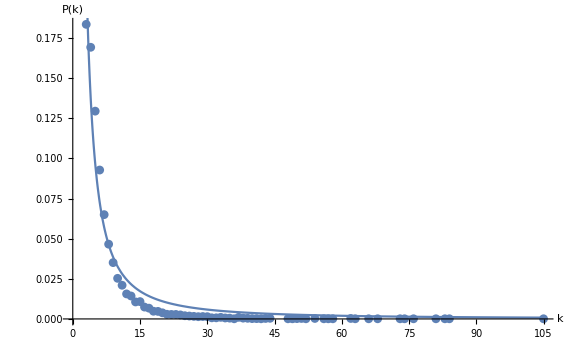

```mathematica
vis4=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large, ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"v-4.eps",vis4];
```

## Mean degree

```mathematica
degree=VertexDegree[igv4]//Mean//N;
```

## Record result

```mathematica
AppendTo[results, Flatten[{"visibility",ToString@n,Length@diffs,degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Horizontal Visibility Graph

```mathematica
horizontals={};Do[
Do[
If[horizontalQ[i,j,diffs],AppendTo[horizontals,i->j],Null],
{j,i+1,Length@diffs}
],
{i,1,Length@diffs-1}];
```

## Graph

```mathematica
h4=Graph[horizontals[[1;;100]], DirectedEdges->False, VertexLabelStyle-> Large, GraphLayout->"CircularEmbedding"];gh4=Overlay[{h4,Style["d=4", FontFamily->"Times"]}, Alignment->Center, ImageSize->Large];
```

```mathematica
Export[NotebookDirectory[]<>"h4.eps", gh4]
```

/Users/blmayer/doctorate/thesis/article/h4.eps

```mathematica
igh4=Graph[horizontals, VertexLabels->"Name",DirectedEdges->False,VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igh4];
```

```mathematica
count = Total[adj]//Counts
```

<|1→2,2→4330,3→2107,5→941,4→1347,6→476,9→128,7→299,8→190,11→47,16→3,10→71,12→27,17→4,13→15,18→2,14→5,15→4,19→1|>

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}][[2;;]]
```

{{2,4330/9999},{3,2107/9999},{5,941/9999},{4,449/3333},{6,476/9999},{9,128/9999},{7,299/9999},{8,190/9999},{11,47/9999},{16,1/3333},{10,71/9999},{12,3/1111},{17,4/9999},{13,5/3333},{18,2/9999},{14,5/9999},{15,4/9999},{19,1/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x];
```

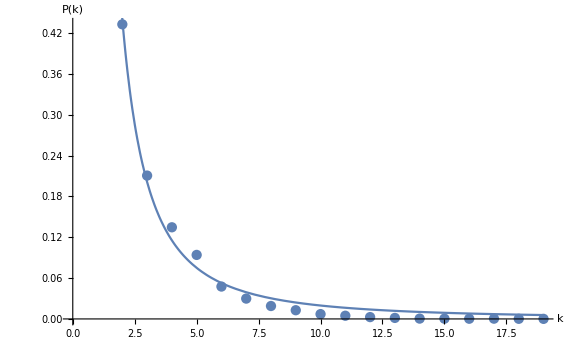

```mathematica
hvis4=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large, ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"hv-4.eps",hvis4];
```

## Mean degree

```mathematica
degree=VertexDegree[igh4]//Mean//N;
```

## Record result

```mathematica
AppendTo[results, Flatten[{"horizontal", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Return result

```mathematica
results
```

{{visibility,4,500,6.128,1.50648 ± 0.242951,1.10629 ± 0.400359},{horizontal,4,500,3.416,1.8667 ± 0.227655,1.59138 ± 0.329767}}